# Agent Network

## Create Base/Seed Network

```mathematica
network[nodes_,conn_]:=Flatten[Table[Table[i->Mod[i+j,nodes,1],{i,1,If[j≥Quotient[nodes+1,2],nodes/2,nodes],1}],{j,1,conn-1,1}]]
```

#### Degree Computation for base network

```mathematica
k = network[100,3];
```

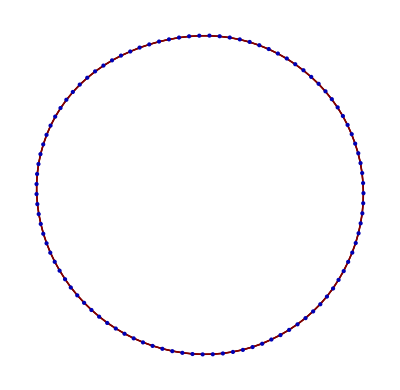

```mathematica
GraphPlot[k,DirectedEdges->False,VertexLabeling->False]
```

```mathematica
Length[k]
```

200

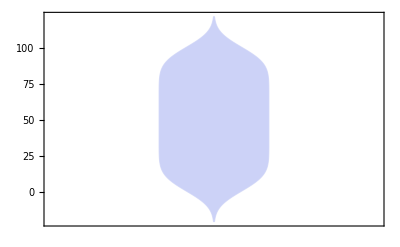

```mathematica
DistributionChart[k]
```

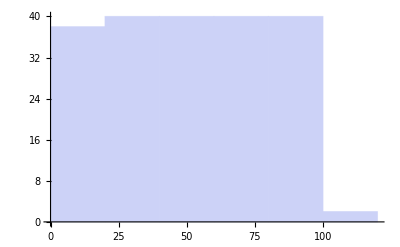

```mathematica
Histogram[k]
```

```mathematica
Needs["Combinatorica`"]
d = For[i = 1, i<Length[k]+1, i++, Distribution[k,{i->j_}]]
```

```mathematica
Distribution[k,{2->j_}]
```

{2}

## Recalibrating connections

```mathematica
network2 = rewirednetwork[p_,network_]:=Table[If[RandomReal[]>p,network[[i]],network[[i]][[1]]->RandomChoice[Cases[network[[All,2]],Except[network[[i]][[1]]]]]],{i,Dimensions[network][[1]]}]
```

```mathematica
k2 = rewirednetwork[0.27,network[10,3]];
```

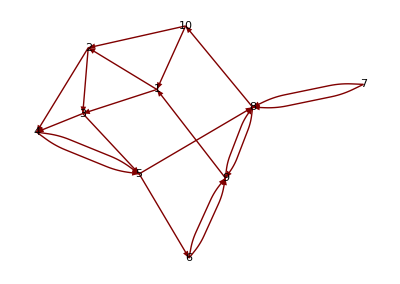

```mathematica
GraphPlot[k2,DirectedEdges->True,VertexLabeling->True]
```

```mathematica
DistributionChart[k2];
Histogram[k2];
```

```mathematica
Needs["GraphUtilities`"]
v = VertexList[k2]
e = EdgeList[k2]
```

{1,2,3,4,5,6,9,7,8,10}

{{1,2},{1,3},{2,3},{2,4},{3,4},{3,5},{4,5},{5,6},{5,8},{6,9},{9,8},{9,1},{7,8},{8,9},{8,10},{10,1},{10,2}}

```mathematica
pr = PageRankVector[k2]
```

{0.108289,0.0941203,0.101024,0.0979364,0.141181,0.0750019,0.141628,0.015,0.147944,0.0778761}

```mathematica
ClosenessCentrality[k2]
```

{0.,0.,0.,0.,0.,0.,0.,0.025641,0.,0.}